```mathematica
a = Table[i,{i,1,6}]
```

{1,2,3,4,5,6}

```mathematica
Sin[a]
```

{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6]}

```mathematica
a a+1
```

{2,5,10,17,26,37}

```mathematica
init = {{1,1},{-1,1},{-1,-1},{1,-1},{1,1}}
```

{{1,1},{-1,1},{-1,-1},{1,-1},{1,1}}

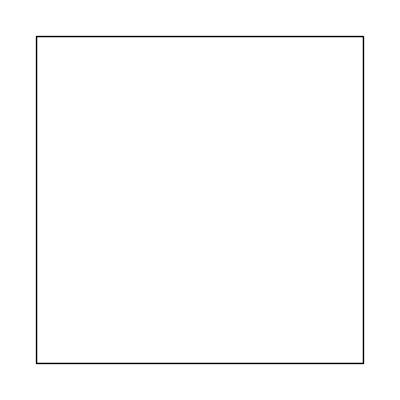

```mathematica
Show[Graphics[Line[init]]]
```

```mathematica
u = {{1/2,-1/2},{1/2,1/2}}
```

```mathematica
{{1/2,-1/2},{1/2,1/2}}
```

{{1/2,-1/2},{1/2,1/2}}

```mathematica
u//MatrixForm
```

(1/2 | -1/2
1/2 | 1/2)

```mathematica
rotate[p_]:=Map[u.#&,p]
```

```mathematica
p1=rotate[init]
```

{{0,1},{-1,0},{0,-1},{1,0},{0,1}}

```mathematica
p2=rotate[p1]
```

{{-1/2,1/2},{-1/2,-1/2},{1/2,-1/2},{1/2,1/2},{-1/2,1/2}}

```mathematica
p3=rotate[p2]
```

{{-1/2,0},{0,-1/2},{1/2,0},{0,1/2},{-1/2,0}}

```mathematica
p4=rotate[p3]
```

{{-1/4,-1/4},{1/4,-1/4},{1/4,1/4},{-1/4,1/4},{-1/4,-1/4}}

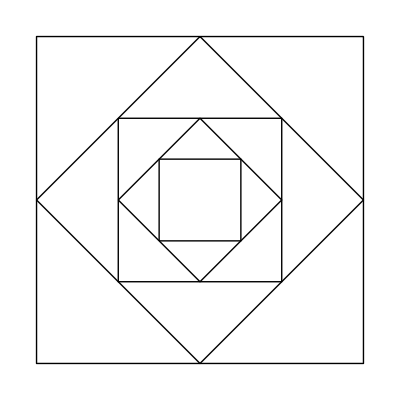

```mathematica
Show[Graphics[Line[{init,p1,p2,p3,p4}]]]
```

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

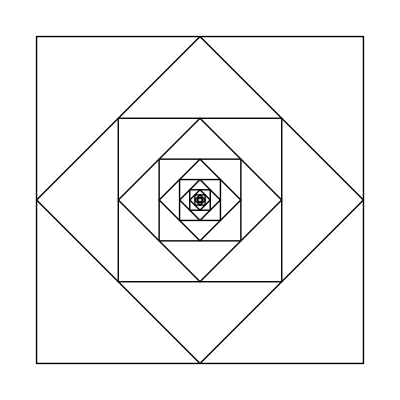

```mathematica
Show[Graphics[Line[NestList[rotate,init,13]]]]
```

```mathematica
MandelbrotSetPlot[]
```

-Graphics-

```mathematica
MandelbrotSetPlot[{-0.3+I,0+0.7I}]
```

-Graphics-

```mathematica
ColorDatapaclet:ref/ColorData[]
```

RefLink[ColorData,paclet:ref/ColorData][]

```mathematica
a[]
```

```mathematica
Clear["Global`*"]
```

```mathematica
mandelbrot[c_]:=
Length[FixedPointList[#^2+c&,0.+0 I,50,SameTest->(Abs[#2]≥2.&)]]
```

```mathematica
DensityPlot[mandelbrot[x+y I],{x,-2,0.5},
{y,-1,1},PlotPoints->100,
ColorFunction->"SunsetColors",
PlotLegends->Automatic]
```

-Graphics-